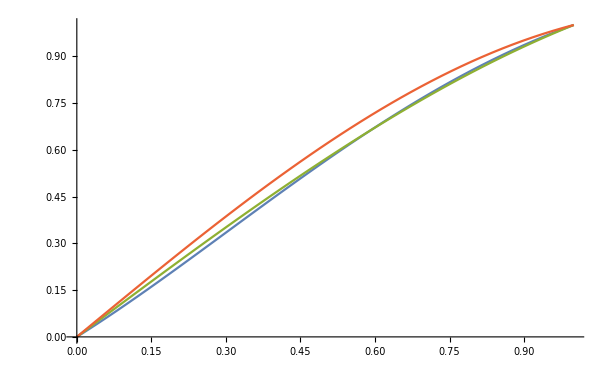

```mathematica
(* this is the definition of g(x) on [0, 1] *)
g[x_]:=x/Gamma[x+1.];

h[x_,n_,k_]:=Sin[k/n x]/Sin[k/n];

(* visualize of some of the functions *)
Plot[{g[x],h[4,3],h[x,4,4],h[x,4,5]},{x,0,1}]
```

The first thing we will try is basis functions that look like this
	s(x,k)=Sin(k/m x)
where  0<=x<=1,  k=1,2,⋯,K  and  m  is chosen by trial and error.

We use ∑_(i=1)^k c_i s(x,k)≈g(x)
To find c_i, multiply this equation by s(x,1) and integrate on [0,1] to get the first equation, then multiply by s(x,2) and integrate on [0,1] to get the second equation, ...
multiply this equation by s(x,k) and integrate on [0,1] to get the k^th equation.

Notice that the maximum error is about 0.0008

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.272676,0.397215,0.321925,0.119412,-0.0713157,-0.14282,-0.0851195,0.0240321,0.0890359,0.0683496},{«20»,«8»,«20»},«7»,{0.0683496,0.0841921,0.0307673,«4»,0.248185,0.416791,0.477176}} may contain significant numerical errors.

{-6509.61,8527.07,-5662.3,1228.36,1524.56,-1917.43,1153.41,-426.437,94.0144,-9.67472}

-6509.61 Sin[1. x]+8527.07 Sin[2. x]-5662.3 Sin[3. x]+1228.36 Sin[4. x]+1524.56 Sin[5. x]-1917.43 Sin[6. x]+1153.41 Sin[7. x]-426.437 Sin[8. x]+94.0144 Sin[9. x]-9.67472 Sin[10. x]

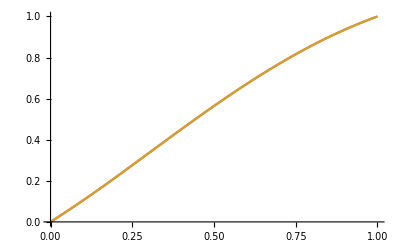

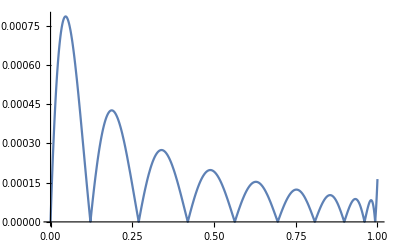

```mathematica
Clear[b,f,g,k]

g[x_]:=x/Gamma[x+1.];

m=1.0;
k=10;
s[x_,k_]:=Sin[k/m x]
a=Table[NIntegrate[s[x,i]s[x,j],{x,0,1}],{j,1,k},{i,1,k}];
r=Table[NIntegrate[g[x]s[x,i],{x,0,1}],{i,1,k}];

c=LinearSolve[a,r]
f[x_]=Sum[c[[i]]s[x,i],{i,1,k}]

Plot[{g[x],f[x]},{x,0,1}]

Plot[Abs[g[x]-f[x]],{x,0,1},PlotRange->All]
```

We do the same thing on with basis functions that look like sin(k/0.5 x) and
K=40.

Notice that the maximum error is about 0.00003

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.5946,0.250609,-0.156435,0.00391643,0.0841921,-0.0625799,-0.0133602,0.0562396,-0.0318206,-0.0206596,«30»},«9»,«30»} may contain significant numerical errors.

4.31176 Sin[2. x]-5.97366 Sin[4. x]+6.44145 Sin[6. x]-5.47474 Sin[8. x]+3.62443 Sin[10. x]-1.72336 Sin[12. x]+0.366908 Sin[14. x]+0.251703 Sin[16. x]-0.318669 Sin[18. x]+0.162023 Sin[20. x]-0.0346614 Sin[22. x]+0.00376813 Sin[24. x]-0.00147304 Sin[26. x]-0.0600248 Sin[28. x]+0.194012 Sin[30. x]-0.334791 Sin[32. x]+0.396694 Sin[34. x]-0.343842 Sin[36. x]+0.211332 Sin[38. x]-0.0744578 Sin[40. x]-0.0063605 Sin[42. x]+0.01914 Sin[44. x]+0.00425686 Sin[46. x]-0.0218908 Sin[48. x]+0.013557 Sin[50. x]+0.00933103 Sin[52. x]-0.0191916 Sin[54. x]-0.0041326 Sin[56. x]+0.0584356 Sin[58. x]-0.122111 Sin[60. x]+0.168643 Sin[62. x]-0.181879 Sin[64. x]+0.162054 Sin[66. x]-0.122055 Sin[68. x]+0.0781442 Sin[70. x]-0.0422733 Sin[72. x]+0.0189299 Sin[74. x]-0.00674645 Sin[76. x]+0.00175094 Sin[78. x]-0.000268923 Sin[80. x]

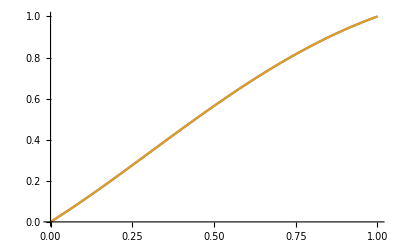

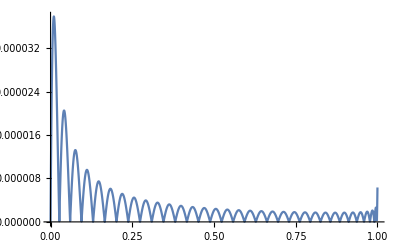

```mathematica
Clear[b,f,g,k]

g[x_]:=x/Gamma[x+1.];

k=40;
b[x_,k_]:=Sin[k/0.5 x];
a=Table[NIntegrate[b[x,i]b[x,j],{x,0,1}],{j,1,k},{i,1,k}];
r=Table[NIntegrate[g[x]b[x,i],{x,0,1}],{i,1,k}];

c=LinearSolve[a,r];
f[x_]=Sum[c[[i]]b[x,i],{i,1,k}]

Plot[{g[x],f[x]},{x,0,1}]

Plot[Abs[g[x]-f[x]],{x,0,1},PlotRange->All]
```

Next we try basis functions that look like this
	s(x,k)=(sin(k/m x))/(sin(k/m))
where  0<=x<=1,  k=1,2,⋯,K  and  m  is chosen by trial and error.

We use ∑_(i=1)^k c_i s(x,k)≈g(x)
To find c_i, let x=x_1 in this equation to get the first equation, let x=x_2 in this equation to get the first equation, ... let x=x_k in this equation to get the k^th equation.

This requires experimenting with m and k, along with x_1,x_2,⋯,x_k

Notice that the maximum error is about 0.0015

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.101857,0.107731,0.118642,0.136777,0.166661,0.218487,0.319771},{0.305119,0.321279,0.351195,0.400662,0.481637,0.620966,0.890928},«4»,{1.,1.,1.,1.,1.,1.,1.}} may contain significant numerical errors.

-4.32173×10^9 Sin[x/3]+5.80466×10^9 Sin[(2 x)/3]-4.40701×10^9 Sin[x]+2.17366×10^9 Sin[(4 x)/3]-6.94434×10^8 Sin[(5 x)/3]+1.3172×10^8 Sin[2 x]-1.13347×10^7 Sin[(7 x)/3]

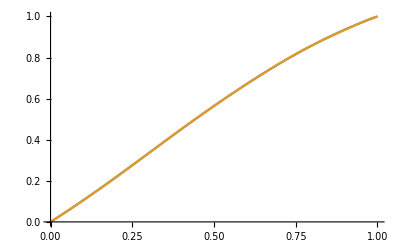

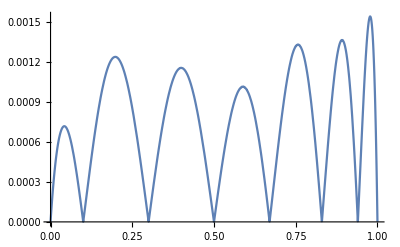

```mathematica
g[x_]:=x/Gamma[x+1.];

h[x_,n_,k_]:=Sin[k/n x]/Sin[k/n];
m=3;
k=7;
x={0.1,0.3,0.5,0.67,0.83,0.94,1.0};
a=Table[h[x[[i]],m,j],{i,1,k},{j,1,k}];
Eigenvalues[a];
b=Table[g[x[[j]]],{j,1,k}];
c=LinearSolve[a,b];

Clear[x]
f[x_]=Sum[c[[i]]h[x,m,i],{i,1,k}]

Plot[{g[x],f[x]},{x,0,1}]

Plot[Abs[g[x]-f[x]],{x,0,1}]
```

We do the same thing as in the previous section with different m and k.

Notice that the maximum error is about 0.0004

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.0949702,0.17521,1.6844,-0.415652,-0.406099,-1.65266,0.808519,0.603619,1.59999,-1.31862,«2»},«9»,«2»} may contain significant numerical errors.

1.20178×10^8 Sin[x]-1.95268×10^8 Sin[2 x]+2.06474×10^8 Sin[3 x]-1.6748×10^8 Sin[4 x]+1.09009×10^8 Sin[5 x]-5.7607×10^7 Sin[6 x]+2.46079×10^7 Sin[7 x]-8.35109×10^6 Sin[8 x]+2.17892×10^6 Sin[9 x]-412407. Sin[10 x]+50606.7 Sin[11 x]-3034.41 Sin[12 x]

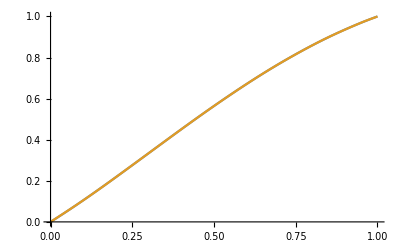

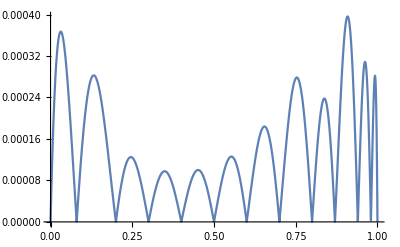

```mathematica
m=1;
k=12;
x={0.08,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.87,0.94,0.98,1.0};
a=Table[h[x[[i]],m,j],{i,1,k},{j,1,k}];
Eigenvalues[a];
b=Table[g[x[[j]]],{j,1,k}];
c=LinearSolve[a,b];

Clear[x]
f[x_]=Sum[c[[i]]h[x,m,i],{i,1,k}]

Plot[{g[x],f[x]},{x,0,1}]

Plot[Abs[g[x]-f[x]],{x,0,1}]
```

We try again with a longer list, hoping to better understand how to avoid the error associated with large coefficients, but it requires a lot of guessing and is not helpful.

```mathematica
m=1;
k=15;
x={0.06,0.15,0.27,0.37,0.48,0.56,0.64,0.7,0.75,0.82,0.88,0.93,0.97,0.99,1.0}
a=Table[h[x[[i]],m,j],{i,1,k},{j,1,k}];
Eigenvalues[a];
b=Table[g[x[[j]]],{j,1,k}];
c=LinearSolve[a,b]

Clear[x]
f[x_]=Sum[c[[i]]h[x,m,i],{i,1,k}];

Plot[{g[x],f[x]},{x,0,1}]

Plot[Abs[g[x]-f[x]],{x,0,1}]
```

Here we try using exact arithmetic. This works fine for values of n<=1, but produces the same errors for n>1.

-3.32168 Sin[2. x]+7.36775 Sin[4. x]-9.49329 Sin[6. x]+9.86588 Sin[8. x]-8.84577 Sin[10. x]+6.96966 Sin[12. x]-4.85737 Sin[14. x]+2.97968 Sin[16. x]-1.59068 Sin[18. x]+0.720994 Sin[20. x]-0.266274 Sin[22. x]+0.073113 Sin[24. x]-0.0118493 Sin[26. x]

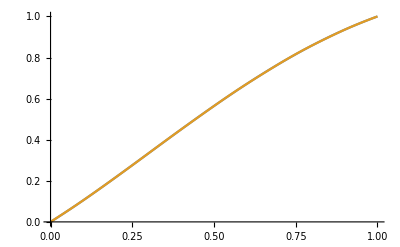

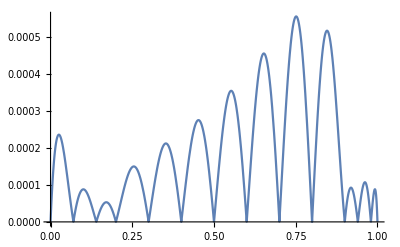

```mathematica
g[x_]:=x/Gamma[x+1.];

h[x_,n_,k_]:=Sin[k/n x]/Sin[k/n];
n=0.5;
k=13;
x={7/100,14/100,20/100,30/100,40/100,50/100,60/100,70/100,80/100,90/100,94/100,98/100,1};
a=Table[h[x[[i]],n,j],{i,1,k},{j,1,k}];
b=Table[g[x[[j]]],{j,1,k}];
c=LinearSolve[a,b];

Clear[x]
f[x_]=Sum[c[[i]]h[x,n,i],{i,1,k}]

Plot[{g[x],f[x]},{x,0,1}]

Plot[Abs[g[x]-f[x]],{x,0,1},PlotRange->All]
```

In this section we compute the Fourier Series of g(x) using the formulas in the Mathematica documentation under FourierSeries.

Because the periodic version of g(x) is discontinuous at the boundaries, the approximation has the expected ringing there as well.

0.701211 Sin[π x]-0.339048 Sin[2 π x]+0.212675 Sin[3 π x]-0.161671 Sin[4 π x]+0.127412 Sin[5 π x]-0.106844 Sin[6 π x]+0.0909765 Sin[7 π x]-0.0798892 Sin[8 π x]+0.0707498 Sin[9 π x]-0.0638214 Sin[10 π x]+0.0578823 Sin[11 π x]-0.0531438 Sin[12 π x]+0.0489754 Sin[13 π x]-0.0455309 Sin[14 π x]+0.0424444 Sin[15 π x]-0.0398276 Sin[16 π x]+0.0374503 Sin[17 π x]-0.0353951 Sin[18 π x]+0.0335078 Sin[19 π x]-0.0318509 Sin[20 π x]+0.0303163 Sin[21 π x]-0.0289522 Sin[22 π x]+0.02768 Sin[23 π x]-0.0265373 Sin[24 π x]+0.0254654 Sin[25 π x]-0.0244944 Sin[26 π x]+0.023579 Sin[27 π x]-0.0227437 Sin[28 π x]+0.0219528 Sin[29 π x]-0.0212266 Sin[30 π x]+0.0205365 Sin[31 π x]-0.0198992 Sin[32 π x]+0.0192918 Sin[33 π x]-0.0187282 Sin[34 π x]+0.0181894 Sin[35 π x]-0.0176873 Sin[36 π x]+0.0172061 Sin[37 π x]-0.0167561 Sin[38 π x]+0.0163238 Sin[39 π x]-0.015918 Sin[40 π x]+0.0155275 Sin[41 π x]-0.0151598 Sin[42 π x]+0.0148052 Sin[43 π x]-0.0144705 Sin[44 π x]+0.0141472 Sin[45 π x]-0.0138412 Sin[46 π x]+0.0135452 Sin[47 π x]-0.0132644 Sin[48 π x]+0.0129923 Sin[49 π x]-0.0127337 Sin[50 π x]

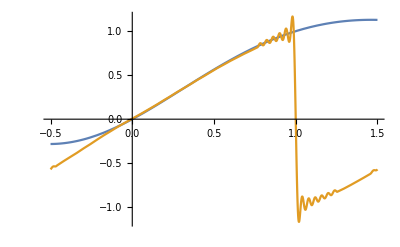

```mathematica
g[x_]=x/Gamma[x+1.];
m=50;
cc=Table[2 NIntegrate[g[x]Sin[π k x],{x,0,1}],{k,1,m}];

f[x_]=Sum[cc[[i]]Sin[π i x],{i,1,m}]

Plot[{g[x],f[x]},{x,-0.5,1.5}]
```

In this section we compute the Taylor series of g(x) centered at c=0.5. Notice that the error can be made as small as desired by increasing the number of terms.

With

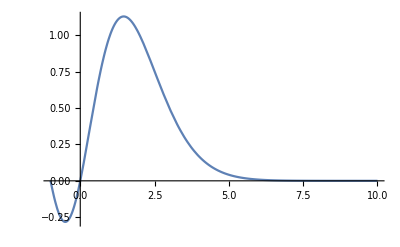

0.56419+1.10779 (x-0.5)-0.304502 (x-0.5)^2-0.439103 (x-0.5)^3+0.200585 (x-0.5)^4+0.0298893 (x-0.5)^5-0.0388487 (x-0.5)^6+0.00767326 (x-0.5)^7+0.00156537 (x-0.5)^8-0.00103455 (x-0.5)^9+0.000165035 (x-0.5)^10+0.0000184068 (x-0.5)^11-0.0000128187 (x-0.5)^12+2.18517×10^-6 (x-0.5)^13+1.33749×10^-8 (x-0.5)^14-8.05838×10^-8 (x-0.5)^15+1.66378×10^-8 (x-0.5)^16-1.06539×10^-9 (x-0.5)^17-2.30753×10^-10 (x-0.5)^18+7.05829×10^-11 (x-0.5)^19-8.05472×10^-12 (x-0.5)^20+O[x-0.5]^21

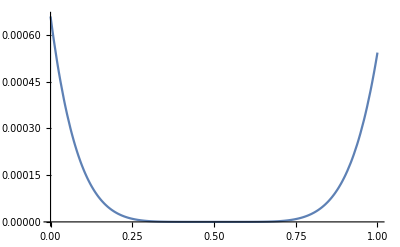

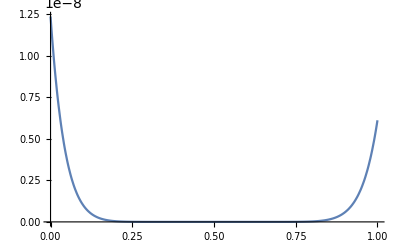

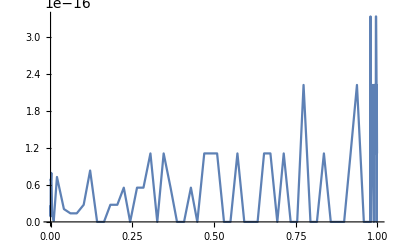

```mathematica
g[x_]:=x/Gamma[x+1.];
Plot[g[x],{x,-1,10}]

m=20;
Series[g[x],{x,0.5,m}]

(* error with m = 5 *)
Plot[Abs[g[x]-(0.5641895835477563+1.107791903872871 (x-0.5)-0.3045017442080552 (x-0.5)^2-0.439103422503577 (x-0.5)^3+0.20058545616778756 (x-0.5)^4+0.02988927556343818 (x-0.5)^5)],{x,0,1},
PlotRange->All]

(* error with m = 10 *)
Plot[Abs[g[x]-(0.5641895835477563+1.107791903872871 (x-0.5)-0.3045017442080552 (x-0.5)^2-0.439103422503577 (x-0.5)^3+0.20058545616778756 (x-0.5)^4+0.02988927556343818 (x-0.5)^5-0.0388487204551235 (x-0.5)^6+0.00767326354811062 (x-0.5)^7+0.0015653663152754784 (x-0.5)^8-0.001034551444211159 (x-0.5)^9+0.00016503522322938743 (x-0.5)^10)],{x,0,1},
PlotRange->All]

(* error with m = 20 *)
Plot[Abs[g[x]-(0.5641895835477563+1.107791903872871 (x-0.5)-0.3045017442080552 (x-0.5)^2-0.439103422503577 (x-0.5)^3+0.20058545616778756 (x-0.5)^4+0.02988927556343818 (x-0.5)^5-0.0388487204551235 (x-0.5)^6+0.00767326354811062 (x-0.5)^7+0.0015653663152754784 (x-0.5)^8-0.001034551444211159 (x-0.5)^9+0.00016503522322938743 (x-0.5)^10+0.000018406802064863893 (x-0.5)^11-0.000012818704072658402 (x-0.5)^12+2.1851746107788437*^-6 (x-0.5)^13+1.3374884951756079*^-8 (x-0.5)^14-8.05837764726146*^-8 (x-0.5)^15+1.6637785092402193*^-8 (x-0.5)^16-1.0653923499306884*^-9 (x-0.5)^17-2.307527490219497*^-10 (x-0.5)^18+7.058291853716337*^-11 (x-0.5)^19-8.054718542448974*^-12 (x-0.5)^20)],{x,0,1},
PlotRange->All]
```

```mathematica
Clear[b,f,g,k]

g[x_]:=x/Gamma[x+1.];

k=40;
b[x_,k_]:=Sin[k/0.5 x]
a=Table[NIntegrate[b[x,i]b[x,j],{x,0,1}],{j,1,k},{i,1,k}];
r=Table[NIntegrate[g[x]b[x,i],{x,0,1}],{i,1,k}];

c=LinearSolve[a,r]
f[x_]=Sum[c[[i]]b[x,i],{i,1,k}]

Plot[{g[x],f[x]},{x,0,1}]

Plot[Abs[g[x]-f[x]],{x,0,1},PlotRange->All]
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.5946,0.250609,-0.156435,0.00391643,0.0841921,-0.0625799,-0.0133602,0.0562396,-0.0318206,-0.0206596,«30»},«9»,«30»} may contain significant numerical errors.

{4.31176,-5.97366,6.44145,-5.47474,3.62443,-1.72336,0.366908,0.251703,-0.318669,0.162023,-0.0346614,0.00376813,-0.00147304,-0.0600248,0.194012,-0.334791,0.396694,-0.343842,0.211332,-0.0744578,-0.0063605,0.01914,0.00425686,-0.0218908,0.013557,0.00933103,-0.0191916,-0.0041326,0.0584356,-0.122111,0.168643,-0.181879,0.162054,-0.122055,0.0781442,-0.0422733,0.0189299,-0.00674645,0.00175094,-0.000268923}

4.31176 Sin[2. x]-5.97366 Sin[4. x]+6.44145 Sin[6. x]-5.47474 Sin[8. x]+3.62443 Sin[10. x]-1.72336 Sin[12. x]+0.366908 Sin[14. x]+0.251703 Sin[16. x]-0.318669 Sin[18. x]+0.162023 Sin[20. x]-0.0346614 Sin[22. x]+0.00376813 Sin[24. x]-0.00147304 Sin[26. x]-0.0600248 Sin[28. x]+0.194012 Sin[30. x]-0.334791 Sin[32. x]+0.396694 Sin[34. x]-0.343842 Sin[36. x]+0.211332 Sin[38. x]-0.0744578 Sin[40. x]-0.0063605 Sin[42. x]+0.01914 Sin[44. x]+0.00425686 Sin[46. x]-0.0218908 Sin[48. x]+0.013557 Sin[50. x]+0.00933103 Sin[52. x]-0.0191916 Sin[54. x]-0.0041326 Sin[56. x]+0.0584356 Sin[58. x]-0.122111 Sin[60. x]+0.168643 Sin[62. x]-0.181879 Sin[64. x]+0.162054 Sin[66. x]-0.122055 Sin[68. x]+0.0781442 Sin[70. x]-0.0422733 Sin[72. x]+0.0189299 Sin[74. x]-0.00674645 Sin[76. x]+0.00175094 Sin[78. x]-0.000268923 Sin[80. x]

-Graphics-

-Graphics-